```mathematica
ode=x-y[x]==0
```

x-y[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→x}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==0},y[x],x]]
```

{{y[x]→x}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

1

```mathematica
dyadx[x_]:=1
```

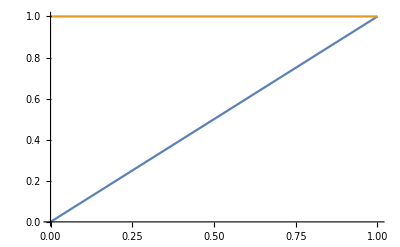

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```